```mathematica
Clear[x,y,a]
```

```mathematica
sol=AsymptoticSolve[(ϵ^2 )x^4+(-4ϵ)x^3-8x^2+1==0,{x},{ϵ,0,5}](*Expansion method*)
```

{{x→-1/(2 √2)-ϵ/32-(7 ϵ^2)/(512 √2)-(7 ϵ^3)/2048-(511 ϵ^4)/(262144 √2)-(39 ϵ^5)/65536},{x→1/(2 √2)-ϵ/32+(7 ϵ^2)/(512 √2)-(7 ϵ^3)/2048+(511 ϵ^4)/(262144 √2)-(39 ϵ^5)/65536},{x→4/((-1-√3) ϵ)+(4 (1/(16 (-1-√3))+7/(64 √3 (-1-√3))) ϵ)/(-1-√3)+(4 (97/(12288 (-1-√3)^2)+7/(512 √3 (-1-√3)^2)+19/(2048 (-1-√3))+395/(24576 √3 (-1-√3))) ϵ^3)/(-1-√3)},{x→4/((-1+√3) ϵ)+(4 (1/(16 (-1+√3))-7/(64 √3 (-1+√3))) ϵ)/(-1+√3)+(4 (97/(12288 (-1+√3)^2)-7/(512 √3 (-1+√3)^2)+19/(2048 (-1+√3))-395/(24576 √3 (-1+√3))) ϵ^3)/(-1+√3)}}

```mathematica
y1[x_]:=-1/(2 √2)-ϵ/32-(7 ϵ^2)/(512 √2)-(7 ϵ^3)/2048-(511 ϵ^4)/(262144 √2)-(39 ϵ^5)/65536
```

```mathematica
y2[x_]:=1/(2 √2)-ϵ/32+(7 ϵ^2)/(512 √2)-(7 ϵ^3)/2048+(511 ϵ^4)/(262144 √2)-(39 ϵ^5)/65536
```

```mathematica
y3[x_]:=4/((-1-√3) ϵ)+(4 (1/(16 (-1-√3))+7/(64 √3 (-1-√3))) ϵ)/(-1-√3)+(4 (97/(12288 (-1-√3)^2)+7/(512 √3 (-1-√3)^2)+19/(2048 (-1-√3))+395/(24576 √3 (-1-√3))) ϵ^3)/(-1-√3)
```

```mathematica
y4[x_]:=4/((-1+√3) ϵ)+(4 (1/(16 (-1+√3))-7/(64 √3 (-1+√3))) ϵ)/(-1+√3)+(4 (97/(12288 (-1+√3)^2)-7/(512 √3 (-1+√3)^2)+19/(2048 (-1+√3))-395/(24576 √3 (-1+√3))) ϵ^3)/(-1+√3)
```

```mathematica
y1[x]/.ϵ->0.1
```

-0.356779

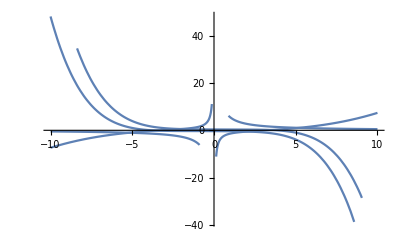

```mathematica
Show[Plot[y1[x],{ϵ,-10,10}],Plot[y2[x],{ϵ,-10,10}],Plot[y3[x],{ϵ,-10,10}],Plot[y4[x],{ϵ,-10,10}]]
```

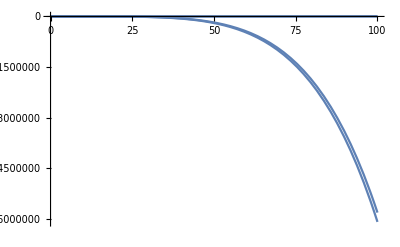

```mathematica
Show[Plot[y1[x],{ϵ,0,100}],Plot[y2[x],{ϵ,0,100}],Plot[y3[x],{ϵ,0,100}],Plot[y4[x],{ϵ,0,100}]]
```

```mathematica
Solve[(ϵ^2 )x^4+(-4ϵ)x^3-8x^2+1==0,x]; (*exact calculations*)
```

```mathematica
x1[ϵ_]:=1/ϵ-1/2 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))-1/2 √(56/(3 ϵ^2)-(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))-(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2)-48/(ϵ^3 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))))
```

```mathematica
x2[ϵ_]:=1/ϵ-1/2 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))+1/2 √(56/(3 ϵ^2)-(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))-(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2)-48/(ϵ^3 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))))
```

```mathematica
x3[ϵ_]:=1/ϵ+1/2 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))-1/2 √(56/(3 ϵ^2)-(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))-(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2)+48/(ϵ^3 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))))
```

```mathematica
x4[ϵ_]:=1/ϵ+1/2 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))+1/2 √(56/(3 ϵ^2)-(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))-(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2)+48/(ϵ^3 √(28/(3 ϵ^2)+(2 (16+3 ϵ^2))/(3 ϵ^2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))+(2 (-64+63 ϵ^2+3 √3 √(-384 ϵ^2+131 ϵ^4-ϵ^6))^(1/3))/(3 ϵ^2))))
```

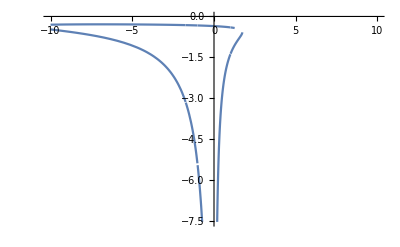

```mathematica
Show[Plot[x1[ϵ],{ϵ,-10,10}],Plot[x2[ϵ],{ϵ,-10,10}],Plot[x3[ϵ],{ϵ,-10,10}],Plot[x4[ϵ],{ϵ,-10,10}]]
```

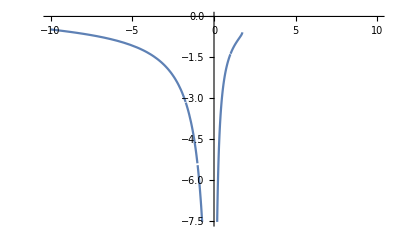

```mathematica
Plot[x1[ϵ],{ϵ,-10,10}]
```

```mathematica
(*dominant balance iterations*)
```

```mathematica
(ϵ^2 )x^4+(-4ϵ)x^3-8x^2+1==0
```

1-8 x^2-4 x^3 ϵ+x^4 ϵ^2==0

```mathematica
f[x_]:=-8/ϵ^2+1/x^2*ϵ^2-x^2
```

```mathematica
NestList[f,x,4]
```

{x,-x^2-8/ϵ^2+ϵ^2/x^2,-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2,-8/ϵ^2+ϵ^2/((-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2)^2)-(-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2)^2,-8/ϵ^2+ϵ^2/((-8/ϵ^2+ϵ^2/((-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2)^2)-(-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2)^2)^2)-(-8/ϵ^2+ϵ^2/((-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2)^2)-(-8/ϵ^2+ϵ^2/((-x^2-8/ϵ^2+ϵ^2/x^2)^2)-(-x^2-8/ϵ^2+ϵ^2/x^2)^2)^2)^2}

```mathematica
x[0]=-8/ϵ^2
```

-8/ϵ^2

```mathematica
a=Table[x[i]=-8/ϵ^2+1/x[i-1]^2*ϵ^2-x[i-1]^2,{i,1,5}];
```

```mathematica
b=Table[x[i]=-1/ϵ^2-(8x[i-1]^2-1)/x[i-1]^3*ϵ^2,{i,1,5}];
c=Table[x[i]=Sqrt[8+Sqrt[64+4*ϵ^2*x[i-1]]/2*ϵ^2],{i,1,5}];
```

```mathematica
a/.ϵ-> 0.1
```

{-640800.,-4.10625×10^11,-1.68613×10^23,-2.84302×10^46,-8.08277×10^92}

```mathematica
b/.ϵ-> 0.1
```

{-99.9999,-99.9992,-99.9992,-99.9992,-99.9992}

```mathematica
c/.ϵ-> 0.1
```

{2.83342,2.8355,2.8355,2.8355,2.8355}

```mathematica
Show[ListPlot[a/.ϵ-> 0.1],ListPlot[b/.ϵ-> 0.1],ListPlot[c/.ϵ-> 0.1]]
```

-Graphics-